```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
U="U=0.333";
range=0.6;
```

```mathematica
ΔμeV=100; (* μeV *)
TmK=30; (* mK *)
TμeV=TmK/11.6; (* μeV *)
T0=TμeV/ΔμeV (* dimensionless *)
T=T0;
```

0.0258621

```mathematica
(* We are computing χ=(χ0 + χ1 factor Exp[-β g])/(1 +factor Exp[-β g]). We set χ1=0. *)
```

```mathematica
prep[Γ_]:=Module[{},
dir=U<>"_Gamma="<>Γ;
l=Import[dir<>"/optical1.dat"];
p1=ListPlot[l,Joined->True];
gap=Interpolation[l];
l=Import[dir<>"/chi1.dat"];
p2=ListPlot[l,Joined->True,PlotRange->{{0,2},{0,6}},LabelStyle->Larger,PlotStyle->Null,
Epilog->Text[Γ,{0.2,5.5}]];
chi=Interpolation[l];
Z[x_]:=1+factor Exp[-gap[x]/T];
chi2[x_]:=chi[x]/Z[x];
chi2[#]&
];
proc[Γ_,scalex_,scaley_]:=Module[{fnc},
fnc=prep[Γ];
Plot[scaley fnc[1+scalex x],{x,-range,range},PlotRange->{All,{0,900}},PlotStyle->Red,Filling->0]
];
```

```mathematica
gammas=Map[StringDrop[#,14]&,FileNames[U<>"*"]]
```

{0.0025,0.005,0.0075,0.00875,0.010,0.01125,0.0125,0.01375,0.015,0.01625,0.0175,0.01875,0.020,0.02125,0.0225,0.02375,0.025,0.02625,0.0275,0.02875,0.030,0.03125,0.0325,0.03375,0.035,0.03625,0.0375,0.03875,0.040,0.0425,0.045,0.0475,0.050,0.0525,0.055,0.0575,0.060,0.070,0.080,0.090,0.100,0.110,0.120,0.140,0.160}

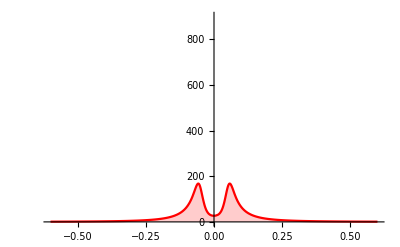
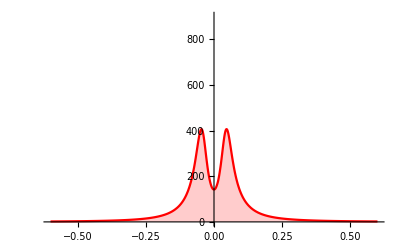
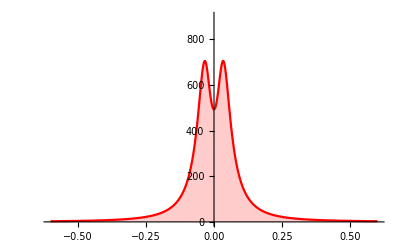
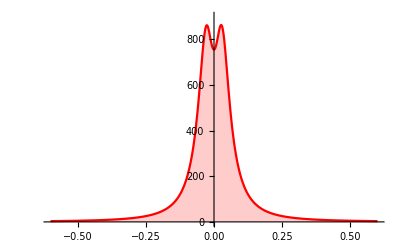
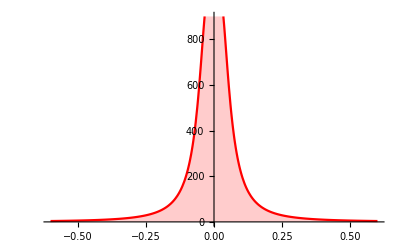
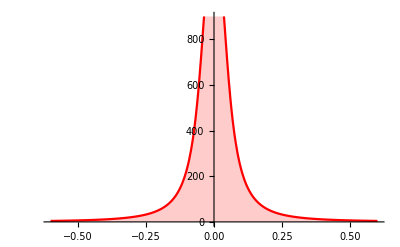
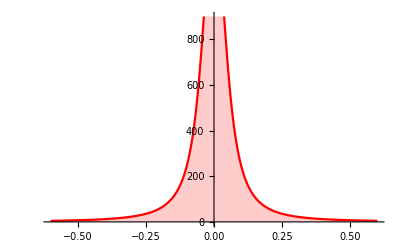
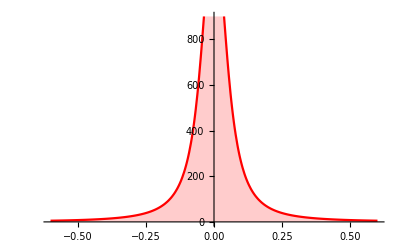

```mathematica
factor=10^4;
pl=Map[proc[#,2,100]&,gammas]
```

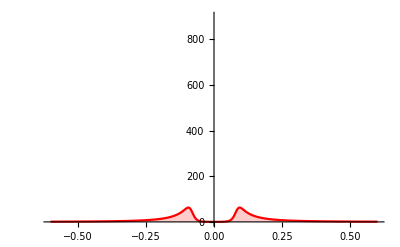
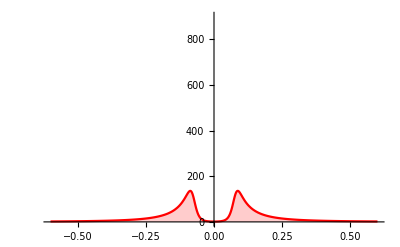
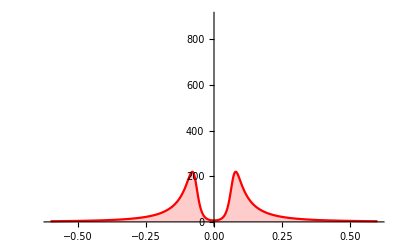
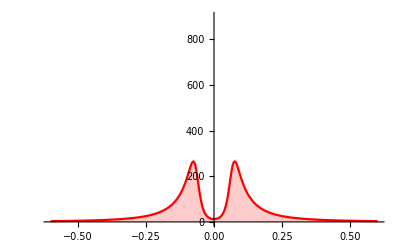
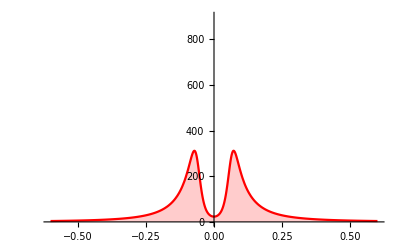
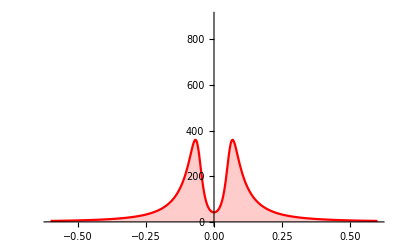
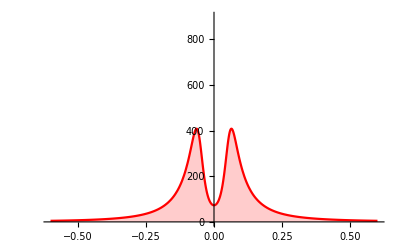
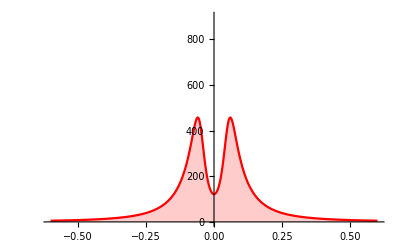
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
factor=10^6;
pl=Map[proc[#,2,100]&,gammas]
```

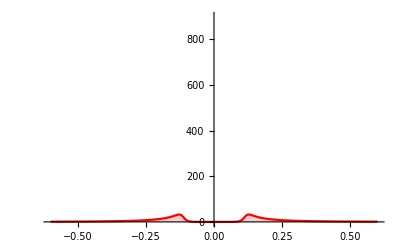
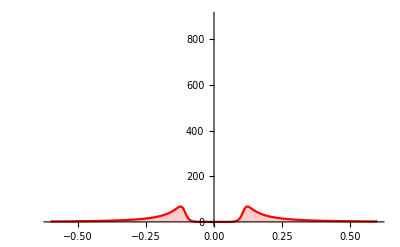
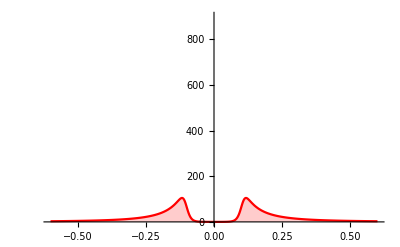
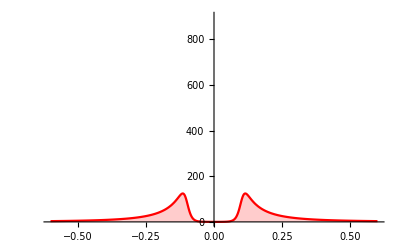
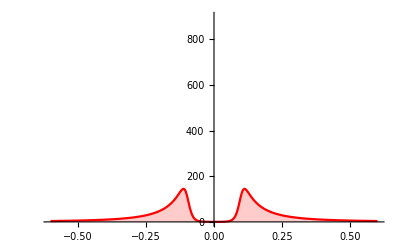
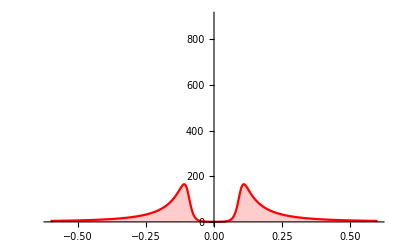
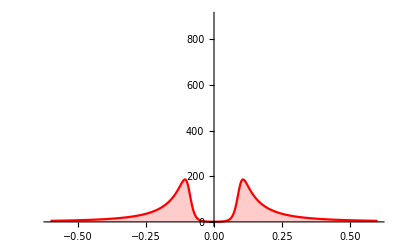
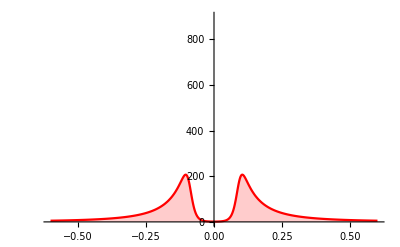
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
factor=10^8;
pl=Map[proc[#,2,100]&,gammas]
```

```mathematica
loadsym[set_]:=Module[{l,l1,l2},
l=Import["../experimental_data/dataset_"<>set<>".csv"];
l=Drop[l,1]; (* header *)
l=l[[All,{1,2}]]; (* gate voltage, quantum capacitance *)
l=Map[{#[[1]]1000,#[[2]]10^18}&,l]; (* mV, aF *)
l=Select[l,-range<First[#]<=(range 1.0001)&]; (* filter range *)
l1=l;
l2=Transpose[{l[[All,1]],Reverse@l[[All,2]]}];
l=(l1+l2)/2;
l
];
plot[set_]:=Module[{l},
l=loadsym[set];
pa=ListPlot[l,PlotRange->{All,{0,500}},Joined->True,Mesh->All]
];
```

```mathematica
scalex=2;
scaley=100;
```

```mathematica
sets={"01","02","03","04","05","06","07","08","09","10","11","12","13","14"}
sets={"05","06","07","08","09","10","11","12","13","14"}
sets={"05","06","07","08","09","10","11","12","13"}
Map[plot[#]&,Reverse[sets]]
```

{01,02,03,04,05,06,07,08,09,10,11,12,13,14}

{05,06,07,08,09,10,11,12,13,14}

{05,06,07,08,09,10,11,12,13}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 
Length[l]
l[[1]]
l[[-1]]
l[[61]]
*)
```

```mathematica
comp[set_,gamma_]:=Module[{},
pa=plot[set];
pb=proc[gamma,scalex,scaley];
Show[pa,pb,PlotRange->All]
];
```

```mathematica
wghtX[x_]:=(1-Abs[x]/range);
weight[set_,gamma_]:=Module[{},
l1=loadsym[set];
fnc0=prep[gamma];
fnc=scaley fnc0[1+scalex #]&;
(* Max[] is used to avoid noise at low values *)
(* No square in denominator? *)
Total@Map[(#[[2]]-fnc[#[[1]]])^2/Max[{20,(#[[2]]+fnc[#[[1]]])/2}]^2*wghtX[#[[1]]]&,l1]
];
```

```mathematica
totalweight=0;
autofit[set_]:=Module[{},
w=Map[{#,weight[set,#]}&,gammas];
w=Sort[w,Last[#1]<Last[#2]&];
totalweight+=w[[1,2]];
w[[1,1]]
];
```

```mathematica
factor=10^8;
scalex=2;
scaley=60;
comp["01",autofit["01"]]
w
```

-Graphics-

{{0.140,5.90241},{0.160,6.24467},{0.120,10.544},{0.110,18.4641},{0.100,32.4785},{0.090,51.23},{0.080,70.9041},{0.070,88.6243},{0.060,103.792},{0.0575,107.266},{0.055,110.65},{0.0525,113.966},{0.050,117.235},{0.0475,120.483},{0.045,123.733},{0.0425,127.01},{0.040,130.341},{0.03875,132.037},{0.0375,133.759},{0.03625,135.51},{0.035,137.293},{0.03375,139.115},{0.0325,140.98},{0.03125,142.894},{0.030,144.863},{0.02875,146.893},{0.0275,148.988},{0.02625,151.151},{0.025,153.39},{0.02375,155.715},{0.0225,158.126},{0.02125,160.628},{0.020,163.229},{0.01875,165.947},{0.0175,168.789},{0.01625,171.747},{0.015,174.834},{0.01375,178.042},{0.0125,181.406},{0.01125,184.944},{0.010,188.671},{0.00875,192.565},{0.0075,196.666},{0.005,205.583},{0.0025,215.551}}

```mathematica
ClearAll[twfnc];
twfnc[a_,b_,c_,d_]/;NumberQ[a]:=Module[{},
totalweight=0;
factor=10^a;
scalex=b;
scaley=c;
T=d;
plots=Map[{best=autofit[#];comp[#,best],w[[1]]}&,sets];
tw=totalweight;
Print[{a,b,c,d,tw}];
tw
];
```

```mathematica
twfnc[9.2,1.06,50.3,0.022]
p1=plots
```

{9.2,1.06,50.3,0.022,29.1077}

29.1077

{{-Graphics-,{0.040,1.5061}},{-Graphics-,{0.0475,2.79652}},{-Graphics-,{0.03125,0.934699}},{-Graphics-,{0.0275,1.21187}},{-Graphics-,{0.0225,10.7766}},{-Graphics-,{0.01875,4.79258}},{-Graphics-,{0.015,1.88512}},{-Graphics-,{0.010,2.5462}},{-Graphics-,{0.00875,2.65802}}}

```mathematica
twfnc[9.8,1.02,50.3,0.020]
p1=plots
```

{9.8,1.02,50.3,0.02,27.5982}

27.5982

{{-Graphics-,{0.040,1.09063}},{-Graphics-,{0.0475,2.18725}},{-Graphics-,{0.02875,0.775843}},{-Graphics-,{0.02625,1.06385}},{-Graphics-,{0.02125,10.4242}},{-Graphics-,{0.0175,4.96237}},{-Graphics-,{0.01375,1.67861}},{-Graphics-,{0.010,2.56841}},{-Graphics-,{0.00875,2.84704}}}

```mathematica
Export["fits.pdf",Reverse[p1]]
```

fits.pdf

```mathematica
dens=10^23 (* atoms per cm^3 *)
smallerfactor=(10^4)^3
dens/smallerfactor
Log[10,%]
```

100000000000000000000000

1000000000000

100000000000

11

```mathematica
sol=FindMinimum[twfnc[a1,b1,c1,d1],{{a1,8,3,10},{b1,1.1,1,2},{c1,50,10,100},{d1,T0,0.5T0,2T0}}]
```

{8.,1.1,50.,0.0258621,34.4521}

{8.,1.1,50.,0.0258621,34.4521}

{8.,1.1,50.,0.0258621,34.4521}

«2 more identical outputs»

{8.,1.1,50.,0.0258621,34.452}

{8.00011,1.09958,50.,0.0517241,276.717}

{8.00011,1.09958,50.,0.0517241,276.717}

{8.00011,1.09958,50.,0.0517241,276.717}

«2 more identical outputs»

{8.00011,1.09958,50.,0.0517242,276.717}

{8.00001,1.09995,50.,0.0286255,39.0809}

{8.00001,1.09995,50.,0.0286255,39.0809}

{8.00001,1.09995,50.,0.0286255,39.0809}

«3 more identical outputs»

{8.,1.09999,50.,0.0265271,34.203}

{8.,1.09999,50.,0.0265271,34.203}

{8.,1.09999,50.,0.0265271,34.203}

«2 more identical outputs»

{8.,1.09999,50.,0.0265272,34.2029}

{8.,1.09998,50.,0.0269795,34.1372}

{8.,1.09998,50.,0.0269795,34.1372}

{8.,1.09998,50.,0.0269795,34.1372}

«2 more identical outputs»

{8.,1.09998,50.,0.0269796,34.1373}

{8.,1.09998,50.,0.0264579,34.5469}

{8.,1.09998,50.,0.0264579,34.5469}

{8.,1.09998,50.,0.0264579,34.5469}

«2 more identical outputs»

{8.,1.09998,50.,0.0264579,34.5468}

{8.,1.09998,50.,0.0267577,33.2905}

{8.,1.09998,50.,0.0267577,33.2905}

{8.,1.09998,50.,0.0267577,33.2905}

«3 more identical outputs»

{8.,1.09998,50.,0.0267648,33.29}

{8.,1.09998,50.,0.0267648,33.29}

{8.,1.09998,50.,0.0267648,33.29}

«3 more identical outputs»

{8.,1.09997,50.,0.0267631,33.2897}

{8.,1.09997,50.,0.0267631,33.2897}

{8.,1.09997,50.,0.0267631,33.2897}

«3 more identical outputs»

{8.00001,1.09995,50.,0.0267595,33.2888}

{8.00001,1.09995,50.,0.0267595,33.2888}

{8.00001,1.09995,50.,0.0267595,33.2888}

«3 more identical outputs»

{8.00001,1.09988,50.,0.026754,33.2866}

{8.00001,1.09988,50.,0.026754,33.2866}

{8.00001,1.09988,50.,0.026754,33.2866}

«3 more identical outputs»

{8.00003,1.09966,50.,0.0267446,33.2808}

{8.00003,1.09966,50.,0.0267446,33.2808}

{8.00003,1.09966,50.,0.0267446,33.2808}

«3 more identical outputs»

{8.00007,1.09906,50.,0.0267289,33.266}

{8.00007,1.09906,50.,0.0267289,33.266}

{8.00007,1.09906,50.,0.0267289,33.266}

«3 more identical outputs»

{8.00018,1.0975,50.0001,0.026703,33.2294}

{8.00018,1.0975,50.0001,0.026703,33.2294}

{8.00018,1.0975,50.0001,0.026703,33.2294}

«3 more identical outputs»

{8.00044,1.09388,50.0002,0.0266645,33.1483}

{8.00044,1.09388,50.0002,0.0266645,33.1483}

{8.00044,1.09388,50.0002,0.0266645,33.1483}

«2 more identical outputs»

{8.00044,1.09388,50.0002,0.0266645,33.1482}

{8.00093,1.08707,50.0004,0.026622,32.9875}

{8.00093,1.08707,50.0004,0.026622,32.9875}

{8.00093,1.08707,50.0004,0.026622,32.9875}

«2 more identical outputs»

{8.00093,1.08707,50.0004,0.026622,32.9874}

{8.00208,1.07112,50.0008,0.0265521,32.7656}

{8.00208,1.07112,50.0008,0.0265521,32.7656}

{8.00208,1.07112,50.0008,0.0265521,32.7656}

«2 more identical outputs»

{8.00208,1.07112,50.0008,0.0265521,32.7655}

{8.00234,1.06759,50.0009,0.0265349,32.764}

{8.00234,1.06759,50.0009,0.0265349,32.764}

{8.00234,1.06759,50.0009,0.0265349,32.764}

«3 more identical outputs»

{8.00224,1.069,50.0009,0.0265466,32.7598}

{8.00224,1.069,50.0009,0.0265466,32.7598}

{8.00224,1.069,50.0009,0.0265466,32.7598}

«3 more identical outputs»

{8.00223,1.06909,50.0009,0.0265511,32.7591}

{8.00223,1.06909,50.0009,0.0265511,32.7591}

{8.00223,1.06909,50.0009,0.0265511,32.7591}

«3 more identical outputs»

{8.00224,1.06894,50.0009,0.0265526,32.7589}

{8.00224,1.06894,50.0009,0.0265526,32.7589}

{8.00224,1.06894,50.0009,0.0265526,32.7589}

«3 more identical outputs»

{8.00224,1.0689,50.0009,0.0265525,32.7589}

{8.00224,1.0689,50.0009,0.0265525,32.7589}

{8.00224,1.0689,50.0009,0.0265525,32.7589}

«3 more identical outputs»

{8.00225,1.06887,50.0009,0.0265524,32.7589}

{8.00225,1.06887,50.0009,0.0265524,32.7589}

{8.00225,1.06887,50.0009,0.0265524,32.7589}

«3 more identical outputs»

{8.00225,1.06882,50.0009,0.0265522,32.7589}

{8.00225,1.06882,50.0009,0.0265522,32.7589}

{8.00225,1.06882,50.0009,0.0265522,32.7589}

«3 more identical outputs»

{8.00227,1.06874,50.0009,0.0265519,32.7589}

{8.00227,1.06874,50.0009,0.0265519,32.7589}

{8.00227,1.06874,50.0009,0.0265519,32.7589}

«3 more identical outputs»

{8.00231,1.06861,50.0009,0.0265513,32.7588}

{8.00231,1.06861,50.0009,0.0265513,32.7588}

{8.00231,1.06861,50.0009,0.0265513,32.7588}

«3 more identical outputs»

{8.00241,1.06839,50.0009,0.0265503,32.7586}

{8.00241,1.06839,50.0009,0.0265503,32.7586}

{8.00241,1.06839,50.0009,0.0265503,32.7586}

«3 more identical outputs»

{8.00267,1.06804,50.001,0.0265482,32.7581}

{8.00267,1.06804,50.001,0.0265482,32.7581}

{8.00267,1.06804,50.001,0.0265482,32.7581}

«3 more identical outputs»

{8.00331,1.06748,50.0011,0.026544,32.7567}

{8.00331,1.06748,50.0011,0.026544,32.7567}

{8.00331,1.06748,50.0011,0.026544,32.7567}

«2 more identical outputs»

{8.00331,1.06748,50.0011,0.0265441,32.7567}

{8.00498,1.06657,50.0014,0.026535,32.753}

{8.00498,1.06657,50.0014,0.026535,32.753}

{8.00498,1.06657,50.0014,0.026535,32.753}

«3 more identical outputs»

{8.00948,1.065,50.0022,0.0265133,32.7432}

{8.00948,1.065,50.0022,0.0265133,32.7432}

{8.00948,1.065,50.0022,0.0265133,32.7432}

«3 more identical outputs»

{8.02636,1.06063,50.0054,0.0264458,32.723}

{8.02636,1.06063,50.0054,0.0264458,32.723}

{8.02636,1.06063,50.0054,0.0264458,32.723}

«3 more identical outputs»

{8.032,1.06085,50.0064,0.0264218,32.6928}

{8.032,1.06085,50.0064,0.0264218,32.6928}

{8.032,1.06085,50.0064,0.0264218,32.6928}

«3 more identical outputs»

{10.,1.13853,50.3637,0.0180446,64.8223}

{10.,1.13853,50.3637,0.0180446,64.8223}

{10.,1.13853,50.3637,0.0180446,64.8223}

«2 more identical outputs»

{10.,1.13853,50.3637,0.0180446,64.8221}

{8.38149,1.07464,50.0699,0.0249341,32.1082}

{8.38149,1.07464,50.0699,0.0249341,32.1082}

{8.38149,1.07464,50.0699,0.0249341,32.1082}

«2 more identical outputs»

{8.38149,1.07464,50.0699,0.0249341,32.1083}

{9.19075,1.10659,50.2168,0.0214893,35.6712}

{9.19075,1.10659,50.2168,0.0214893,35.6712}

{9.19075,1.10659,50.2168,0.0214893,35.6711}

{9.19075,1.10659,50.2168,0.0214893,35.6712}

{9.19075,1.10659,50.2168,0.0214893,35.6712}

{9.19075,1.10659,50.2168,0.0214894,35.671}

{8.65947,1.08562,50.1203,0.0237508,30.981}

{8.65947,1.08562,50.1203,0.0237508,30.981}

{8.65947,1.08562,50.1203,0.0237508,30.981}

«2 more identical outputs»

{8.65947,1.08562,50.1203,0.0237508,30.9809}

{8.79914,1.06481,50.1461,0.0231406,30.1968}

{8.79914,1.06481,50.1461,0.0231406,30.1968}

{8.79914,1.06481,50.1461,0.0231406,30.1968}

«3 more identical outputs»

{8.6936,1.,50.1278,0.0236392,33.1633}

{8.6936,1.,50.1278,0.0236392,33.1633}

{8.6936,1.,50.1278,0.0236392,33.1633}

«2 more identical outputs»

{8.6936,1.,50.1278,0.0236392,33.1634}

{8.77283,1.04865,50.1415,0.0232649,29.6895}

{8.77283,1.04865,50.1415,0.0232649,29.6895}

{8.77283,1.04865,50.1415,0.0232649,29.6895}

«3 more identical outputs»

{8.83333,1.04799,50.1525,0.0230353,29.579}

{8.83333,1.04799,50.1525,0.0230353,29.579}

{8.83333,1.04799,50.1525,0.0230353,29.579}

«3 more identical outputs»

{9.07533,1.04534,50.1967,0.0221171,29.5327}

{9.07533,1.04534,50.1967,0.0221171,29.5327}

{9.07533,1.04534,50.1967,0.0221171,29.5327}

«2 more identical outputs»

{9.07533,1.04534,50.1967,0.0221171,29.5328}

{10.,1.03523,50.3652,0.0186085,32.3426}

{10.,1.03523,50.3652,0.0186085,32.3426}

{10.,1.03523,50.3652,0.0186085,32.3426}

«2 more identical outputs»

{10.,1.03523,50.3652,0.0186085,32.3424}

{9.43012,1.04146,50.2613,0.0207708,28.8531}

{9.43012,1.04146,50.2613,0.0207708,28.8531}

{9.43012,1.04146,50.2613,0.0207708,28.8531}

«2 more identical outputs»

{9.43012,1.04146,50.2613,0.0207708,28.853}

{9.19719,1.04401,50.2189,0.0216547,29.0124}

{9.19719,1.04401,50.2189,0.0216547,29.0124}

{9.19719,1.04401,50.2189,0.0216547,29.0124}

«2 more identical outputs»

{9.19719,1.04401,50.2189,0.0216547,29.0125}

{9.34689,1.04237,50.2461,0.0210867,28.3695}

{9.34689,1.04237,50.2461,0.0210867,28.3695}

{9.34689,1.04237,50.2461,0.0210867,28.3695}

«1 more identical outputs»

{9.34689,1.04237,50.2462,0.0210867,28.3695}

{9.34689,1.04237,50.2461,0.0210867,28.3694}

{9.33636,1.04249,50.2442,0.0211266,28.3625}

{9.33636,1.04249,50.2442,0.0211266,28.3625}

{9.33636,1.04249,50.2442,0.0211266,28.3625}

«3 more identical outputs»

{10.,1.02349,50.3654,0.018604,30.8145}

{10.,1.02349,50.3654,0.018604,30.8145}

{10.,1.02349,50.3654,0.018604,30.8145}

«2 more identical outputs»

{10.,1.02349,50.3654,0.018604,30.8144}

{9.46441,1.03882,50.2676,0.0206398,29.1176}

{9.46441,1.03882,50.2676,0.0206398,29.1176}

{9.46441,1.03882,50.2676,0.0206398,29.1176}

«2 more identical outputs»

{9.46441,1.03882,50.2676,0.0206399,29.1174}

{9.34631,1.0422,50.246,0.0210888,28.3584}

{9.34631,1.0422,50.246,0.0210888,28.3584}

{9.34631,1.0422,50.246,0.0210888,28.3584}

«3 more identical outputs»

{9.40002,1.03089,50.256,0.020932,27.8567}

{9.40002,1.03089,50.256,0.020932,27.8567}

{9.40002,1.03089,50.256,0.020932,27.8567}

«2 more identical outputs»

{9.40002,1.03089,50.256,0.0209321,27.8566}

{9.46247,1.01937,50.2675,0.0207536,27.6791}

{9.46247,1.01937,50.2675,0.0207536,27.6791}

{9.46247,1.01937,50.2675,0.0207536,27.6791}

«3 more identical outputs»

{9.46974,1.01925,50.2689,0.0207383,27.6741}

{9.46974,1.01925,50.2689,0.0207383,27.6741}

{9.46974,1.01925,50.2689,0.0207383,27.6741}

«3 more identical outputs»

{9.58078,1.01888,50.2891,0.0204854,27.6244}

{9.58078,1.01888,50.2891,0.0204854,27.6244}

{9.58078,1.01888,50.2891,0.0204854,27.6244}

«3 more identical outputs»

{9.73834,1.0197,50.3178,0.0201193,27.5854}

{9.73834,1.0197,50.3178,0.0201193,27.5854}

{9.73834,1.0197,50.3178,0.0201193,27.5854}

«3 more identical outputs»

{9.78719,1.0213,50.3267,0.0200148,27.581}

{9.78719,1.0213,50.3267,0.0200148,27.581}

{9.78719,1.0213,50.3267,0.0200148,27.581}

«3 more identical outputs»

{9.78373,1.02125,50.326,0.0200239,27.5808}

{9.78373,1.02125,50.326,0.0200239,27.5808}

{9.78373,1.02125,50.326,0.0200239,27.5808}

«3 more identical outputs»

{9.78764,1.02114,50.3267,0.0200152,27.5808}

{9.78764,1.02114,50.3267,0.0200152,27.5808}

{9.78764,1.02114,50.3267,0.0200152,27.5808}

«3 more identical outputs»

{9.79069,1.02113,50.3273,0.0200085,27.5808}

{9.79069,1.02113,50.3273,0.0200085,27.5808}

{9.79069,1.02113,50.3273,0.0200085,27.5808}

«3 more identical outputs»

{9.79084,1.02113,50.3273,0.0200081,27.5808}

{9.79084,1.02113,50.3273,0.0200081,27.5808}

{9.79084,1.02113,50.3273,0.0200081,27.5808}

«2 more identical outputs»

{9.79084,1.02113,50.3273,0.0200082,27.5808}

{9.79069,1.02113,50.3273,0.0200085,27.5808}

{9.79069,1.02113,50.3273,0.0200085,27.5808}

{9.79069,1.02113,50.3273,0.0200085,27.5808}

«105 more identical outputs»

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{27.5808,{a1→9.79069,b1→1.02113,c1→50.3273,d1→0.0200085}}

```mathematica
tab=Table[{xx,twfnc[xx,1.06,50.3,0.022]},{xx,6,12,0.1}]
ListPlot[tab]
```

{6.,1.06,50.3,0.022,187.458}

{6.1,1.06,50.3,0.022,179.869}

{6.2,1.06,50.3,0.022,174.779}

{6.3,1.06,50.3,0.022,169.073}

{6.4,1.06,50.3,0.022,156.052}

{6.5,1.06,50.3,0.022,143.215}

{6.6,1.06,50.3,0.022,132.846}

{6.7,1.06,50.3,0.022,125.869}

{6.8,1.06,50.3,0.022,121.296}

{6.9,1.06,50.3,0.022,117.909}

{7.,1.06,50.3,0.022,114.681}

{7.1,1.06,50.3,0.022,102.421}

{7.2,1.06,50.3,0.022,91.4959}

{7.3,1.06,50.3,0.022,83.7184}

{7.4,1.06,50.3,0.022,77.7945}

{7.5,1.06,50.3,0.022,75.4465}

{7.6,1.06,50.3,0.022,73.9263}

{7.7,1.06,50.3,0.022,68.1757}

{7.8,1.06,50.3,0.022,61.8365}

{7.9,1.06,50.3,0.022,57.3493}

{8.,1.06,50.3,0.022,54.857}

{8.1,1.06,50.3,0.022,54.099}

{8.2,1.06,50.3,0.022,48.2728}

{8.3,1.06,50.3,0.022,43.9065}

{8.4,1.06,50.3,0.022,40.8156}

{8.5,1.06,50.3,0.022,40.7683}

{8.6,1.06,50.3,0.022,40.0559}

{8.7,1.06,50.3,0.022,36.1687}

{8.8,1.06,50.3,0.022,34.2475}

{8.9,1.06,50.3,0.022,33.1424}

{9.,1.06,50.3,0.022,34.2286}

{9.1,1.06,50.3,0.022,33.4863}

{9.2,1.06,50.3,0.022,32.3127}

{9.3,1.06,50.3,0.022,31.8984}

{9.4,1.06,50.3,0.022,32.6532}

{9.5,1.06,50.3,0.022,34.8907}

{9.6,1.06,50.3,0.022,32.5019}

{9.7,1.06,50.3,0.022,33.128}

{9.8,1.06,50.3,0.022,35.7182}

{9.9,1.06,50.3,0.022,40.2703}

{10.,1.06,50.3,0.022,39.6557}

{10.1,1.06,50.3,0.022,38.6001}

{10.2,1.06,50.3,0.022,38.4933}

{10.3,1.06,50.3,0.022,42.5405}

{10.4,1.06,50.3,0.022,44.7385}

{10.5,1.06,50.3,0.022,46.7532}

{10.6,1.06,50.3,0.022,48.309}

{10.7,1.06,50.3,0.022,52.213}

{10.8,1.06,50.3,0.022,58.2795}

{10.9,1.06,50.3,0.022,63.2303}

{11.,1.06,50.3,0.022,59.7453}

{11.1,1.06,50.3,0.022,60.2221}

{11.2,1.06,50.3,0.022,63.5222}

{11.3,1.06,50.3,0.022,67.0201}

{11.4,1.06,50.3,0.022,73.0919}

{11.5,1.06,50.3,0.022,76.709}

{11.6,1.06,50.3,0.022,79.8566}

{11.7,1.06,50.3,0.022,77.8789}

{11.8,1.06,50.3,0.022,79.1785}

{11.9,1.06,50.3,0.022,82.773}

{12.,1.06,50.3,0.022,87.7927}

{{6.,187.458},{6.1,179.869},{6.2,174.779},{6.3,169.073},{6.4,156.052},{6.5,143.215},{6.6,132.846},{6.7,125.869},{6.8,121.296},{6.9,117.909},{7.,114.681},{7.1,102.421},{7.2,91.4959},{7.3,83.7184},{7.4,77.7945},{7.5,75.4465},{7.6,73.9263},{7.7,68.1757},{7.8,61.8365},{7.9,57.3493},{8.,54.857},{8.1,54.099},{8.2,48.2728},{8.3,43.9065},{8.4,40.8156},{8.5,40.7683},{8.6,40.0559},{8.7,36.1687},{8.8,34.2475},{8.9,33.1424},{9.,34.2286},{9.1,33.4863},{9.2,32.3127},{9.3,31.8984},{9.4,32.6532},{9.5,34.8907},{9.6,32.5019},{9.7,33.128},{9.8,35.7182},{9.9,40.2703},{10.,39.6557},{10.1,38.6001},{10.2,38.4933},{10.3,42.5405},{10.4,44.7385},{10.5,46.7532},{10.6,48.309},{10.7,52.213},{10.8,58.2795},{10.9,63.2303},{11.,59.7453},{11.1,60.2221},{11.2,63.5222},{11.3,67.0201},{11.4,73.0919},{11.5,76.709},{11.6,79.8566},{11.7,77.8789},{11.8,79.1785},{11.9,82.773},{12.,87.7927}}

-Graphics-

```mathematica
tab=Table[{xx,twfnc[9.2,xx,50.3,0.022]},{xx,0.5,1.5,0.05}]
ListPlot[tab]
```

{9.2,0.5,50.3,0.022,262.916}

{9.2,0.55,50.3,0.022,244.697}

{9.2,0.6,50.3,0.022,222.712}

{9.2,0.65,50.3,0.022,196.979}

{9.2,0.7,50.3,0.022,165.637}

{9.2,0.75,50.3,0.022,130.507}

{9.2,0.8,50.3,0.022,99.4032}

{9.2,0.85,50.3,0.022,74.5706}

{9.2,0.9,50.3,0.022,54.8512}

{9.2,0.95,50.3,0.022,40.7497}

{9.2,1.,50.3,0.022,33.5784}

{9.2,1.05,50.3,0.022,32.0152}

{9.2,1.1,50.3,0.022,34.4702}

{9.2,1.15,50.3,0.022,42.3404}

{9.2,1.2,50.3,0.022,54.2261}

{9.2,1.25,50.3,0.022,70.4494}

{9.2,1.3,50.3,0.022,87.0261}

{9.2,1.35,50.3,0.022,106.35}

{9.2,1.4,50.3,0.022,128.29}

{9.2,1.45,50.3,0.022,150.478}

{9.2,1.5,50.3,0.022,172.326}

{{0.5,262.916},{0.55,244.697},{0.6,222.712},{0.65,196.979},{0.7,165.637},{0.75,130.507},{0.8,99.4032},{0.85,74.5706},{0.9,54.8512},{0.95,40.7497},{1.,33.5784},{1.05,32.0152},{1.1,34.4702},{1.15,42.3404},{1.2,54.2261},{1.25,70.4494},{1.3,87.0261},{1.35,106.35},{1.4,128.29},{1.45,150.478},{1.5,172.326}}

-Graphics-

```mathematica
tab=Table[{xx,twfnc[9.2,1.06,xx,0.022]},{xx,30,100,2}]
ListPlot[tab]
```

{9.2,1.06,30,0.022,123.583}

{9.2,1.06,32,0.022,103.788}

{9.2,1.06,34,0.022,87.3459}

{9.2,1.06,36,0.022,73.688}

{9.2,1.06,38,0.022,62.0145}

{9.2,1.06,40,0.022,53.0817}

{9.2,1.06,42,0.022,46.3995}

{9.2,1.06,44,0.022,40.9646}

{9.2,1.06,46,0.022,36.8819}

{9.2,1.06,48,0.022,34.464}

{9.2,1.06,50,0.022,32.5607}

{9.2,1.06,52,0.022,31.0008}

{9.2,1.06,54,0.022,30.4639}

{9.2,1.06,56,0.022,31.1283}

{9.2,1.06,58,0.022,32.8318}

{9.2,1.06,60,0.022,35.3882}

{9.2,1.06,62,0.022,37.7785}

{9.2,1.06,64,0.022,40.7905}

{9.2,1.06,66,0.022,43.5679}

{9.2,1.06,68,0.022,46.1801}

{9.2,1.06,70,0.022,48.9122}

{9.2,1.06,72,0.022,51.1216}

{9.2,1.06,74,0.022,53.8878}

{9.2,1.06,76,0.022,57.158}

{9.2,1.06,78,0.022,60.7687}

{9.2,1.06,80,0.022,64.4726}

{9.2,1.06,82,0.022,68.5749}

{9.2,1.06,84,0.022,72.9873}

{9.2,1.06,86,0.022,77.3732}

{9.2,1.06,88,0.022,81.6386}

{9.2,1.06,90,0.022,86.0088}

{9.2,1.06,92,0.022,90.6324}

{9.2,1.06,94,0.022,95.0381}

{9.2,1.06,96,0.022,99.6784}

{9.2,1.06,98,0.022,104.531}

{9.2,1.06,100,0.022,109.319}

{{30,123.583},{32,103.788},{34,87.3459},{36,73.688},{38,62.0145},{40,53.0817},{42,46.3995},{44,40.9646},{46,36.8819},{48,34.464},{50,32.5607},{52,31.0008},{54,30.4639},{56,31.1283},{58,32.8318},{60,35.3882},{62,37.7785},{64,40.7905},{66,43.5679},{68,46.1801},{70,48.9122},{72,51.1216},{74,53.8878},{76,57.158},{78,60.7687},{80,64.4726},{82,68.5749},{84,72.9873},{86,77.3732},{88,81.6386},{90,86.0088},{92,90.6324},{94,95.0381},{96,99.6784},{98,104.531},{100,109.319}}

-Graphics-

```mathematica
tab=Table[{xx,twfnc[9.2,1.06,50.3,xx]},{xx,0.5T0,2T0,0.025T0}]
ListPlot[tab]
(* 
fnc=a+b(x-x0)^2
sol=FindFit[tab,fnc,{{a,10000},{b,1000},{x0,0.02}},x]
fnc=fnc/.sol;
(x0/.sol)/T0
Show[ListPlot[tab],Plot[fnc,{x,0,0.05}]]
*)
```

{9.2,1.06,50.3,0.012931,215.612}

{9.2,1.06,50.3,0.0135776,194.578}

{9.2,1.06,50.3,0.0142241,176.88}

{9.2,1.06,50.3,0.0148707,144.649}

{9.2,1.06,50.3,0.0155172,128.983}

{9.2,1.06,50.3,0.0161638,115.452}

{9.2,1.06,50.3,0.0168103,90.7445}

{9.2,1.06,50.3,0.0174569,81.1373}

{9.2,1.06,50.3,0.0181034,66.7388}

{9.2,1.06,50.3,0.01875,57.3279}

{9.2,1.06,50.3,0.0193966,48.0624}

{9.2,1.06,50.3,0.0200431,40.9439}

{9.2,1.06,50.3,0.0206897,35.7941}

{9.2,1.06,50.3,0.0213362,33.8646}

{9.2,1.06,50.3,0.0219828,32.3152}

{9.2,1.06,50.3,0.0226293,33.281}

{9.2,1.06,50.3,0.0232759,34.3825}

{9.2,1.06,50.3,0.0239224,40.9376}

{9.2,1.06,50.3,0.024569,39.7044}

{9.2,1.06,50.3,0.0252155,49.041}

{9.2,1.06,50.3,0.0258621,51.6259}

{9.2,1.06,50.3,0.0265086,65.8367}

{9.2,1.06,50.3,0.0271552,66.6992}

{9.2,1.06,50.3,0.0278017,75.4374}

{9.2,1.06,50.3,0.0284483,87.3876}

{9.2,1.06,50.3,0.0290948,89.4227}

{9.2,1.06,50.3,0.0297414,101.755}

{9.2,1.06,50.3,0.0303879,107.111}

{9.2,1.06,50.3,0.0310345,115.525}

{9.2,1.06,50.3,0.031681,126.193}

{9.2,1.06,50.3,0.0323276,130.373}

{9.2,1.06,50.3,0.0329741,140.361}

{9.2,1.06,50.3,0.0336207,144.885}

{9.2,1.06,50.3,0.0342672,155.482}

{9.2,1.06,50.3,0.0349138,161.979}

{9.2,1.06,50.3,0.0355603,168.989}

{9.2,1.06,50.3,0.0362069,178.784}

{9.2,1.06,50.3,0.0368534,185.566}

{9.2,1.06,50.3,0.0375,192.572}

{9.2,1.06,50.3,0.0381466,205.778}

{9.2,1.06,50.3,0.0387931,210.064}

{9.2,1.06,50.3,0.0394397,214.294}

{9.2,1.06,50.3,0.0400862,225.637}

{9.2,1.06,50.3,0.0407328,234.077}

{9.2,1.06,50.3,0.0413793,235.753}

{9.2,1.06,50.3,0.0420259,243.241}

{9.2,1.06,50.3,0.0426724,253.29}

{9.2,1.06,50.3,0.043319,255.764}

{9.2,1.06,50.3,0.0439655,260.686}

{9.2,1.06,50.3,0.0446121,270.957}

{9.2,1.06,50.3,0.0452586,278.473}

{9.2,1.06,50.3,0.0459052,281.906}

{9.2,1.06,50.3,0.0465517,290.027}

{9.2,1.06,50.3,0.0471983,296.404}

{9.2,1.06,50.3,0.0478448,304.086}

{9.2,1.06,50.3,0.0484914,317.819}

{9.2,1.06,50.3,0.0491379,330.352}

{9.2,1.06,50.3,0.0497845,347.352}

{9.2,1.06,50.3,0.050431,372.15}

{9.2,1.06,50.3,0.0510776,402.962}

{9.2,1.06,50.3,0.0517241,435.391}

{{0.012931,215.612},{0.0135776,194.578},{0.0142241,176.88},{0.0148707,144.649},{0.0155172,128.983},{0.0161638,115.452},{0.0168103,90.7445},{0.0174569,81.1373},{0.0181034,66.7388},{0.01875,57.3279},{0.0193966,48.0624},{0.0200431,40.9439},{0.0206897,35.7941},{0.0213362,33.8646},{0.0219828,32.3152},{0.0226293,33.281},{0.0232759,34.3825},{0.0239224,40.9376},{0.024569,39.7044},{0.0252155,49.041},{0.0258621,51.6259},{0.0265086,65.8367},{0.0271552,66.6992},{0.0278017,75.4374},{0.0284483,87.3876},{0.0290948,89.4227},{0.0297414,101.755},{0.0303879,107.111},{0.0310345,115.525},{0.031681,126.193},{0.0323276,130.373},{0.0329741,140.361},{0.0336207,144.885},{0.0342672,155.482},{0.0349138,161.979},{0.0355603,168.989},{0.0362069,178.784},{0.0368534,185.566},{0.0375,192.572},{0.0381466,205.778},{0.0387931,210.064},{0.0394397,214.294},{0.0400862,225.637},{0.0407328,234.077},{0.0413793,235.753},{0.0420259,243.241},{0.0426724,253.29},{0.043319,255.764},{0.0439655,260.686},{0.0446121,270.957},{0.0452586,278.473},{0.0459052,281.906},{0.0465517,290.027},{0.0471983,296.404},{0.0478448,304.086},{0.0484914,317.819},{0.0491379,330.352},{0.0497845,347.352},{0.050431,372.15},{0.0510776,402.962},{0.0517241,435.391}}

-Graphics-

```mathematica
sol=FindMinimum[twfnc[a1,b1,c1,d1],{{a1,6,3,10},{b1,1.31,1,2},{c1,53.2,10,100},{d1,0.85T0,0.5T0,2T0}}]
```

```mathematica
(* sol *)
(* twfnc@@({a1,b1,c1,d1}/.sol[[2]]) *)
(*
twfnc@@({4.2,1.41,60.2,0.03471}/.sol[[2]])
plots
*)
```

```mathematica
rnd[]:=Module[{},
a1=RandomReal[6+{-1,1}];
b1=RandomReal[1.3+0.3{-1,1}];
c1=RandomReal[100+50{-1,1}];
{twfnc[a1,b1,c1],{a1,b1,c1}}
];
(* all=Table[rnd[],{100}] *)
```

```mathematica
(* 
opt=Sort[all][[1]]
factor=10^opt[[2,1]];
scalex=opt[[2,2]];
scaley=opt[[2,3]];
plots=Map[{best=autofit[#];comp[#,best],w[[1]]}&,sets];
tw=totalweight;
plots
tw
*)
```